```mathematica
ResourceFunction["MaTeXInstall"][]
```

Paclet[MaTeX,1.7.9,<>]

```mathematica
(**constants**)
hbar =6.582119569*10^-16;  (* [eV] *)
```

```mathematica
(** Parameters **)
we=0.9326;  (* [eV] *)
wc=we-20*10^-3;  (* [eV] *)
γe=2*67.5*10^-3;  (* [eV] *)
gamc = 6.075*10^-10*γe (*γc=2*0.9*10^-8;  (* [eV] *)*)
g=0.332*10^-3;  (* [eV] *)
v={0.0010,0.0015,0.10,0.25,0.50,1.0}*2(γe/2);
(* dressed parameters *)
(*Ωe[ω_]:=we - g^2(wc-ω)/((wc-ω)^2+(γc/2)^2)
Γe[ω_]:=γe + g^2(γc)/((wc-ω)^2+(γc/2)^2)
Δe[ω_]:=(Ωe[ω]-ω) - (ⅈ*Γe[ω]/2)*)
Δe[ω_]:=(we-ω)-(ⅈ*γe/2)
Δc[ω_,γc_]:=(wc-ω)-(ⅈ*γc/2)
(* Fano parameters *)
ζe[ω_]:=g^2 / ((ω-we)^2+(γe/2)^2)
Ωc[ω_]:=wc + ζe[ω]*(ω-we)
```

8.20125×10^-11

```mathematica
(** calculate the average photon number **)
(*modsqβ[ω_]:=Abs[v/Δe[ω]]^2*)
modsqβ[ω_,γc_]:=Abs[(Δc[ω,γc]*v)/(Δc[ω,γc]*Δe[ω]-g^2)]^2
```

```mathematica
modsqβ[we,gamc]
modsqβ[Ωc[wc],gamc]
```

{4.×10^-6,9.×10^-6,0.04,0.25,1.,4.}

{3.22808×10^-7,7.26319×10^-7,0.00322808,0.0201755,0.0807021,0.322808}

```mathematica
(** calculate the average photon number transmitted through the coupled cavity **)
(* modsqα[ω_,γc_]:=modsqβ[ω,γc] / Abs[ Δc[ω,γc] ]^2 *)
modsqα[ω_,γc_]:=Abs[g* v / (Δc[ω,γc]*Δe[ω]-g^2) ]^2
modsqα[we,gamc]
modsqα[Ωc[wc],gamc]
```

{1.10224×10^-9,2.48004×10^-9,0.0000110224,0.00006889,0.00027556,0.00110224}

{0.179852,0.404667,1798.52,11240.7,44963.,179852.}

```mathematica
(** Poisson distribution **)
p[n_,ω_]:=modsqβ[ω,gamc]^n*Exp[-modsqβ[ω,gamc]]/n!
pplt={p[n,we][[1]],
p[n,we][[2]],
p[n,we][[3]],
p[n,we][[4]]}
```

{(0.999996 (4.×10^-6)^n)/(n!),(0.999991 (9.×10^-6)^n)/(n!),(0.960789 0.04^n)/(n!),(0.778801 0.25^n)/(n!)}

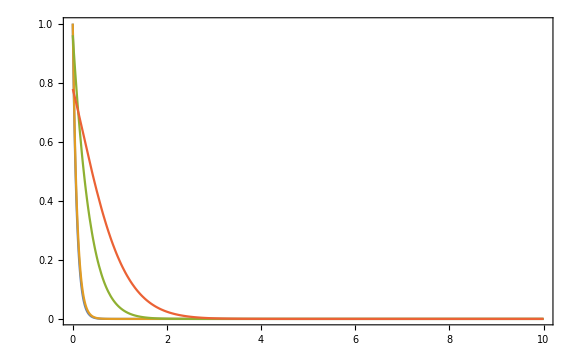

```mathematica
(** plot **)
Plot[pplt,{n,0,10},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"p(n; \\omega=\\omega_e)",None},{"n",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotRange->{{0,10},{0,1}},
PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{
"\\vert \\beta \\vert ^{2} = 0.12","\\vert \\beta \\vert ^{2} = 0.20","\\vert \\beta \\vert ^{2} = 0.04",
"\\vert \\beta \\vert ^{2} = 0.25"(*,
"\\vert \\beta \\vert ^{2} = 1",
"\\vert \\beta \\vert ^{2} = 4"*)},{0.89,0.7}],
ImageSize->Large]
```

```mathematica
pα[n_,ω_]:=modsqα[ω,gamc]^n*Exp[-modsqα[ω,gamc]]/n!
pαplt={pα[n,Ωc[wc]][[1]],
pα[n,Ωc[wc]][[2]],
pα[n,Ωc[wc]][[3]]}
```

General::munfl: Exp[-1798.52] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11240.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44963.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{(0.835394 0.179852^n)/(n!),(0.667199 0.404667^n)/(n!),0.}

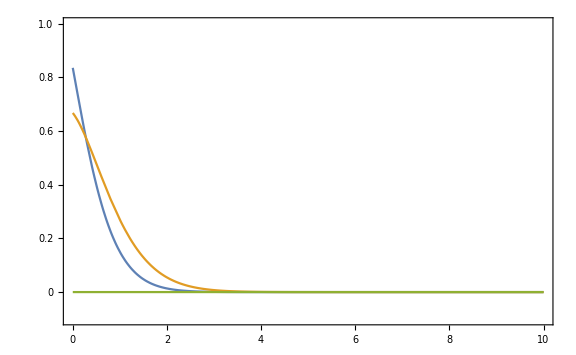

```mathematica
Plot[pαplt,{n,0,10},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"p(n; \\omega=\\omega_e)",None},{"n",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotRange->{{0,10},{-0.1,1}},
PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{"\\vert \\alpha \\vert ^{2} = 0.04",
"\\vert \\alpha \\vert ^{2} = 0.25",
"\\vert \\alpha \\vert ^{2} = 1798"},{0.89,0.7}],
ImageSize->Large]
```

```mathematica
(** The second order correlation of light transmitted through the cavity at steady state**)
G2α[ω_,γc_]:= modsqα[ω,γc]^2
```

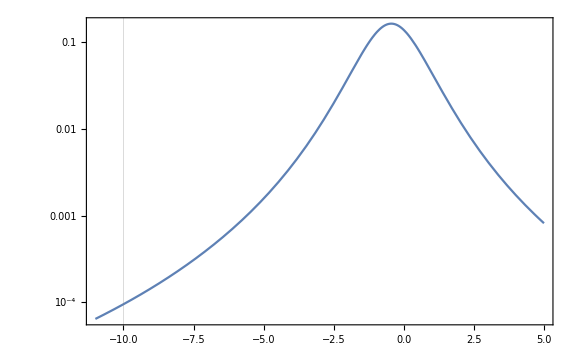

```mathematica
(* plot G2 *)
(*G2αplt=*)
(*G2α[(Δ*10^-3+Ωc[wc])];*)
LogPlot[{G2α[(Δ*10^-6+wc),gamc][[2]]},
{Δ,-11,5},
GridLines->{{{((we-20.01*10^-3)-wc)*10^6,Thick}}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"\\mathrm{Log}[ G^{(2)}_{\\alpha}(\\omega)]",None},{"\\omega - \\omega_c \\: [\\mu eV]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
(*PlotRange->{{-11,5},{0,2.04001*10^8}},*)
PlotRange->All, Exclusions->None,
(*PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{"\\vert \\beta \\vert ^{2} = 0.04",
"\\vert \\beta \\vert ^{2} = 0.25",
"\\vert \\beta \\vert ^{2} = 1",
"\\vert \\beta \\vert ^{2} = 4"},{0.89,0.7}],*)
ImageSize->Large]
```

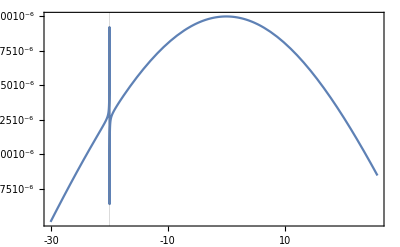

```mathematica
(** Plot average occupation number in emitter and cavity **)
Plot[(*{modsqβ[(Δ*10^-3+we),gamc][[2]]/modsqβ[(0+we),gamc][[2]],
modsqα[(Δ*10^-3+we),gamc][[2]]/modsqα[((Ωc[wc]-we)+we),gamc][[2]]},
 {Δ,-20.1,-19.9},*)
{modsqβ[(Δ*10^-3+we),gamc][[2]](*,
modsqα[(Δ*10^-3+we),gamc][[2]]*)},
 {Δ,-30.1,25.9},
GridLines->{{{(wc-we)*10^3,Thick}}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"\\text{Normalized }N(\\omega)",None},{"\\omega - \\omega_e \\: [m eV]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
(*PlotRange->{{-3,-1},{0,9.37505*10^10}}*)
PlotRange->All, Exclusions->None
(*ImageSize->Small*)]
```

```mathematica
G2α[(-10*10^-6+wc),gamc][[2]]
```

0.0000950106

## Time dynamics

```mathematica
(*time dependent parameter*)
Δct[ω_,t_]:=Δc[ω,gamc]-g^2/Δe[ω]*(1-Exp[-ⅈ*Δe[ω]*t])
```

```mathematica
(*coherent state amplitude*)
(*coupled discrete cavity*)
α[ω_,t_]:=-g*v[[2]]/Δe[ω]*Conjugate[ (Exp[-ⅈ*Δct[ω,t]*t]-1)/Δct[ω,t] ]
(*driven broad-band emitter*)
β[ω_,t_]:=-v[[2]]/Δe[ω]*Conjugate[ 
(Exp[-ⅈ*Δe[ω]*t]-1)/Δe[ω]
+g^2/(Δe[ω]-Δct[ω,t])*
(  (Exp[-ⅈ*Δe[ω]*t]-1)/Δe[ω]
-(Exp[-ⅈ*Δct[ω,t]*t]-1)/Δct[ω,t] )
]
```

Spectrum of the Average Occupation Number

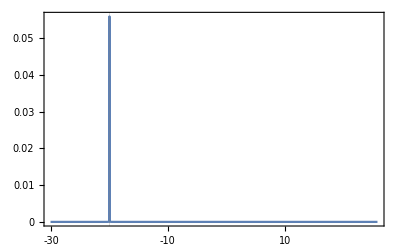

```mathematica
(* spectrum of average occupation number in the cavity*)
Plot[{Abs[α[(Δ*10^-3+we),Infinity]]^2},
 {Δ,-30.1,25.9},
GridLines->{{{(wc-we)*10^3,Thick}}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"\\text{Normalized }N(\\omega)",None},{"\\omega - \\omega_e \\: [m eV]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotRange->All, Exclusions->None]
```

```mathematica
Plot[Abs[α[(1*10^-3+we),(hbar/γe/2)*x]]^2,{x,0,30*10^20}]
```

-Graphics-

```mathematica
Abs[α[(1*10^-3+we),Infinity]]^2
```

2.24898×10^-9

```mathematica
modsqα[(1*10^-3+we),gamc][[2]]
```

2.24898×10^-9

```mathematica
hbar/(γe/2)
```

9.75129×10^-15

```mathematica
hbar/(gamc/2)
```

0.0000160515

```mathematica
hbar/(gamc/2)/hbar/(γe/2)
```

3.61282×10^11

The Second Order Correlation

```mathematica
(* second order correlation *)
G2tα[na_,ω_,t1_,t2_]:= 
(na(na-1)+na(Abs[α[ω,t1]]^2+Abs[α[ω,t2]]^2+2*Re[ Conjugate[α[ω,t1]]*α[ω,t2] ]) +
Abs[α[ω,t1]]^2*Abs[α[ω,t2]]^2
)/(na+Abs[α[ω,0]]^2)^2
```